### Adaptively achieving a goal

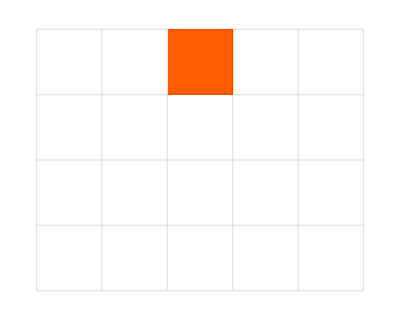
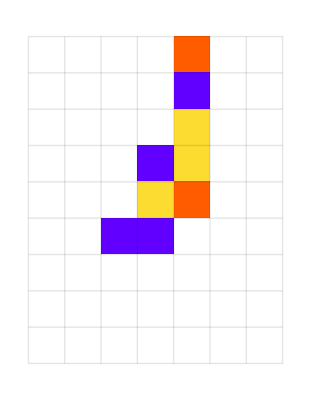
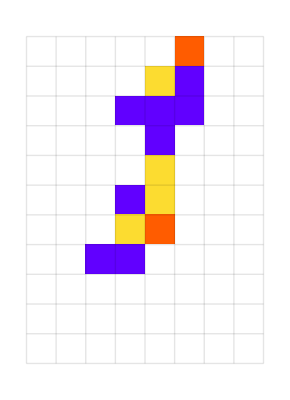
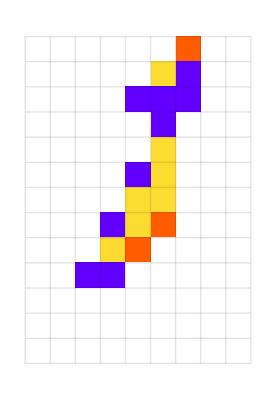
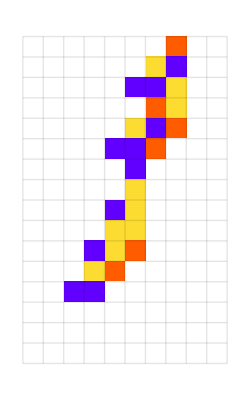
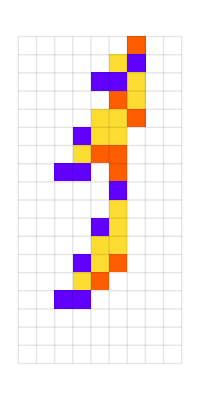
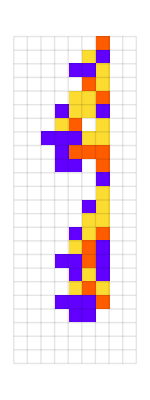
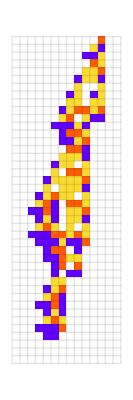

```mathematica
Module[
{deep=500,cut=100,ru,life},
SeedRandom[426781];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,4,1},0},deep];
evo2=Rest[First/@SplitBy[evo,Last]];
Map[CompoundExpression[
data=CellularAutomaton[
First[#],{{1},0},Last[#]+2],
data=ArrayPad[#,2]&/@data,
ArrayPlot[data,ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,26Sqrt[Length[data]+1]},
Mesh->True,MeshStyle->Opacity[.1]
]
]&,
evo2]
]
```

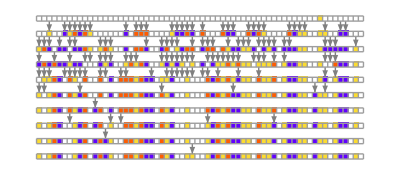

```mathematica
{{"[◼]", "RulesMutationPlot"}}[evo2[[All, 1]]]
```

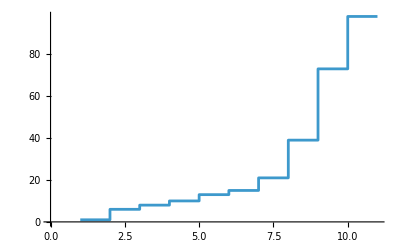

```mathematica
ListStepPlot[evo2[[All, 2]]]
```

### Achieving a goal despite an uncertain environment

#### Loading

```mathematica
k4rob =Select[ , Last[#]>100&];
```

```mathematica
k4reg= Select[,Last[#]>100&];
```

#### Regular organism for comparison

```mathematica
PlotCA[[k4reg[[10, 1]],{{1},0},{200, {-200, 200}},1]]
```

-Graphics-

```mathematica
PlotCA[ResourceFunction["PerturbedCellularAutomaton"][k4reg[[10, 1]],{{1},0},{200, {-200, 200}}, {100, 3}, "Body"->True]]
```

-Graphics-

#### Robust “organism”

```mathematica
PlotCA[ResourceFunction["PerturbedCellularAutomaton"][{299459058088077823758143088095350287424,4,1},{{1},0},{200, {-200, 200}}, {{50, 5}, {52,3}}, "Body"->True]]
```

-Graphics-

```mathematica
PlotCA[ResourceFunction["PerturbedCellularAutomaton"][{299459058088077823758143088095350287424,4,1},{{1},0},{200, {-200, 200}}, 3, "Body"->True]]
```

-Graphics-

### More machine-learning-like example

https://writings.stephenwolfram.com/2024/08/whats-really-going-on-in-machine-learning-some-minimal-models/

### M + D

```mathematica
GraphicsRow[Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={200,{-110,110}},aps,pca,ca,lt},ca={{"[◼]", "PerturbedCellularAutomaton"}}[ru,init,txspec,{}];
{{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {105, {-110, 110}},<||>],"Trim"->{3,None},ImageSize->{Automatic,500},Mesh->True,MeshStyle->Opacity[.1]],{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {105, {-110, 110}},<|{23,111}->2|>],"Trim"->{3,None},ImageSize->{Automatic,500},Mesh->True,MeshStyle->Opacity[.1]],
Spacer[50],
{{"[◼]", "TherapySensitivityPlot"}}[ru, init, txspec,<|{23,111}->2|>, "MaxLength"->105, Mesh->True, MeshStyle->Opacity[.1], ImageSize->{Automatic, 500}],
ArrayPlot[Table[Table[x,4],{x,1,106}], ColorFunctionScaling->True,MeshStyle->Opacity[0.1], ColorFunction->(If[#< .225, LightGray,If[#==1,Darker[Red],
Blend[Reverse@{Orange, Lighter[Orange, .2], Lighter[Orange, .4],  Lighter[Yellow, .7]},#-.225]]]&), Mesh->{True, False} ,ImageSize->{Automatic, 505}, PlotRangePadding->{None, .4}]}], ImageSize->{500, Automatic}, Alignment->Top]
```

```mathematica
{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {105, {-110, 110}},<|{23,111}->2, {46, 107}->"Random"|>]]
```

-Graphics-

```mathematica
Table[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {300, {-110, 110}},<|{23,111}->2, {i, 107}->"Random"|>]], {i, 50, 60}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}